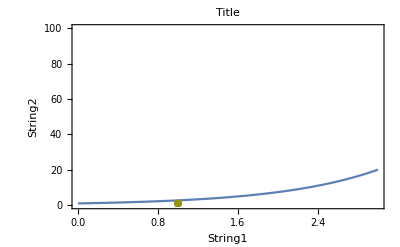

```mathematica
SetDirectory["/home/ethan/spring20/comphys/week4/quiz/"];
res = ReadList["!./a.out",{Number}(*Number, Number,...*) ];
x1 = 0;
x2 = 3;
y1 = 0;
y2 = 100;
xlabel = "String1";
ylabel = "String2";
title = "Title";
simplelistplot = ListPlot[res, Frame->True, PlotRange->{{x1, x2}, {y1,y2}},FrameLabel->{xlabel, ylabel}];
simpleplot = Plot[Exp[x],{x,0,3},PlotRange-> {{x1,x2},{y1,y2}}];
Show[simplelistplot, simpleplot, PlotLabel-> title]
```